```mathematica
ClearAll[tex,tf,mf,df,primeQpos,tr,u,id, bnTab,faulhaber,divisorProduct, jordanTotient];
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
nc[n_]:=N[n]//Chop
ht[n_]:=HoldForm[n]//TraditionalForm
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQpos[n_]:=If[PrimeQ[n]&&n>0,True,False]
tr:=Trace
u[m_Integer]:=1
id[m_Integer]:=Floor[1/m]
bnTab[j_]:=Table[Binomial[n,k],{n,0,j},{k,0,n}]
faulhaber[m_,n_]:=Simplify[1/(m+1)(BernoulliB[m+1,n+1]-BernoulliB[m+1,1])]
divisorProduct[n_,fun_]:=Apply[Times,Map[fun[#]&,Divisors[n]]]
jordanTotient[n_Integer?Positive,k_:1]:=DivisorSum[n,#^k*MoebiusMu[n/#]&];
```

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes MMA

Misscellaneous

## Code

### Self-printing code

#### Example

```mathematica
Print["Hello World"]
```

Hello World

```mathematica
Print[ToString[#0][]]&[]
```

Print[ToString[#0][]] & []

## Functions

### Lagrange Interpolation

#### Example

```mathematica
f[z_]:=InterpolatingPolynomial[{{1,I},{1+I,2I},{I,3I},{2+I,4I}},z]
f[2+I]
```

User Interface

## Manipulate

### Definition / Theorem

#### Example

## PatternTest and Condition

### Definition / Theorem

#### Example

```mathematica
{1,2,3,0.4,0, 0.1, 0.2,2,3,4,5}/.x_?(0≤#≤1&)->999
```

{999,2,3,999,999,999,999,2,3,4,5}

```mathematica
f[x_,y_]/;(x+y<10):=x*y
f[2,5]
f[3,7]
```

10

f[3,7]

## FinancialData

```mathematica
FinancialData["Indices"]
```

{^DJI,^DJUSCH,^DJUSRE,^DXY,^MID,^SGX,^SPX,^NDX,^COMP,^NYA,^SP500TR,^XAX,^000001,^000002,^000003,^399106,^399107,^399108,^AEX,^AMX,^ATX,^BEL,^BTK,^BUX,^BVSP,^CSE,^CSEC,^DAX,^EFEI,^EFON,^HSCEI,^HSI,^HUI,^IBEX,^JKSE,^KLSE,^KSI,^KSIC,^MDAX,^MERV,^MXX,^NIFTY,^NKY,^NZD,^OBX,^PX1,^RTS,^SENSEX,^SET50,^SMI,^STI,^SX5E,^TOPX,^TWII,^VALUA,^VALUG,^VDAX,^VSTX,^XAO,^XJO,^XOI}

## Dynamic

```mathematica
Dynamic[HorizontalGauge[Dynamic[x],{0,range}],TrackedSymbols:>{range}]

Slider[Dynamic[range],{5,50}]
```

## Other

```mathematica
$CloudCreditsAvailable
```

205000

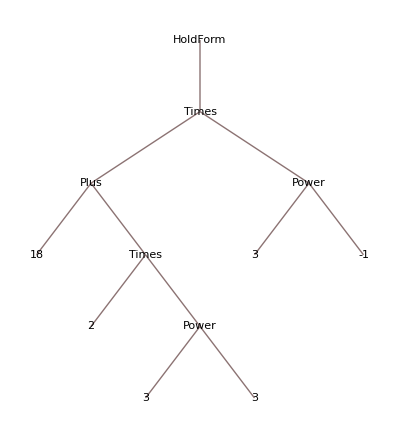

```mathematica
TreeForm[HoldForm[(18+2 3^3)/3]]
```

## Coordinate Systems

```mathematica
CoordinateTransformData["Polar"->"Cartesian","Mapping", {r,θ}]
CoordinateTransformData["Cartesian" -> "Polar","Mapping", {x,y}]

CoordinateTransformData["Spherical" -> "Cartesian","Mapping", {r,θ,ϕ}]
CoordinateTransformData["Cartesian" -> "Spherical","Mapping", {x,y,z}]

CoordinateTransformData["Cylindrical" -> "Cartesian","Mapping", {r,θ,z}]
CoordinateTransformData["Cartesian" -> "Cylindrical","Mapping", {x,y,z}]
```

{r Cos[θ],r Sin[θ]}

{√(0.+y^2),ArcTan[0.,y]}

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

{√(0.+y^2+z^2),ArcTan[z,√(0.+y^2)],ArcTan[0.,y]}

{r Cos[θ],r Sin[θ],z}

{√(0.+y^2),ArcTan[0.,y],z}

```mathematica
data=CoordinateTransformData[]//tf;
```